```mathematica
T = (1/2)*m*v^2
```

(m v^2)/2

```mathematica
U=(1/2*k*q^2)
```

(k q^2)/2

```mathematica
FF=(1/2)*f*v^2
```

(f v^2)/2

```mathematica
L=T-U
```

-(k q^2)/2+(m v^2)/2

```mathematica
a1=D[L, q]
```

-k q

```mathematica
a2=D[L,v]
```

m v

```mathematica
a2t=D[a2,q]*v+D[a2, v]*a
```

a m

```mathematica
a3=D[FF, v]
```

f v

```mathematica
eq=a2t-a1+a3==u
```

a m+k q+f v==u

```mathematica
eqq=eq/.{q->q[t], v->D[q[t],t],a->D[q[t],{t, 2}], u->u[t]}
```

k q[t]+f q'[t]+m q''[t]==u[t]

```mathematica
eqqq=eqq/.{m->1, f->1, k->1}
```

q[t]+q'[t]+q''[t]==u[t]

```mathematica
tf=10
```

10

```mathematica
kp=400
```

400

```mathematica
kd=10(*2*Sqrt[kd]*)
```

10

```mathematica
sol=NDSolve[{eqqq,q[0]==0, q'[0]==0, u[t]==-kd*q'[t]-kp*(q[t]-Sin[t])}, {q}, {t, 0, tf}]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{q→InterpolatingFunction[…]}}

```mathematica
(q[t]/.sol) /.t->2
```

{0.920045}

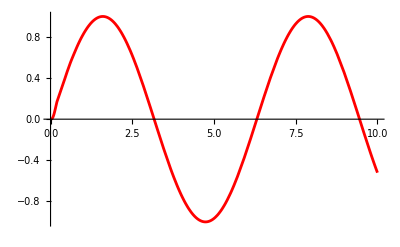

```mathematica
P1=Plot[Evaluate[q[t]/.sol], {t, 0, tf}, PlotRange->All, PlotStyle->Directive[Red]]
```

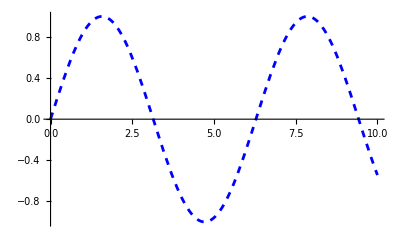

```mathematica
P2=Plot[Sin[t], {t, 0, tf}, PlotRange->All, PlotStyle->Directive[Blue, Dashed]]
```

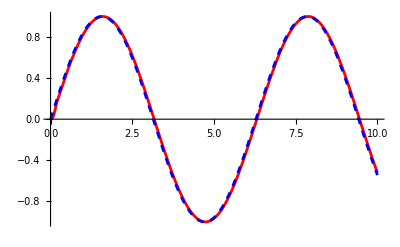

```mathematica
Show[P1,P2]
```

```mathematica
(s+a)^2 // Expand
```

a^2+2 a s+s^2